```mathematica
Table[If[Max[VertexDegree[ReadGrof[k]]]==10,Print[k];Interrupt[]],{k,10000}]
```

1386

$Aborted

```mathematica
ChromaticPolynomial[ReadGrof[3],x]
```

-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6

```mathematica
Factor[-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6]
```

(-3+x)^3 (-2+x) (-1+x) x

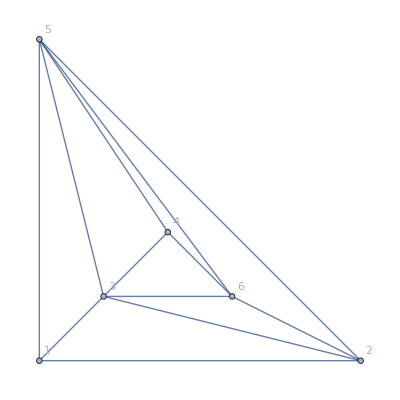

```mathematica
Graph[ReadGrof[3],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

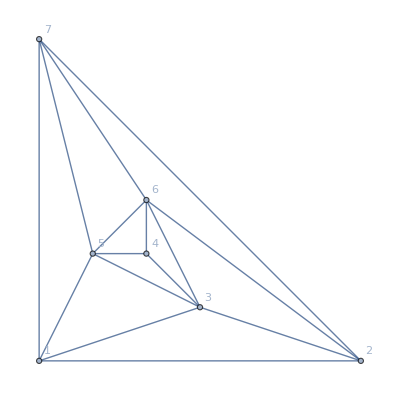

```mathematica
Graph[ReadGrof[6],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

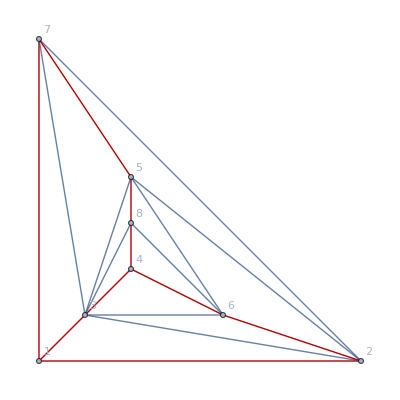

```mathematica
With[{g=Graph[ReadGrof[12],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Graph[g,GraphHighlight-> CollectMPGEdges[g]]]
```

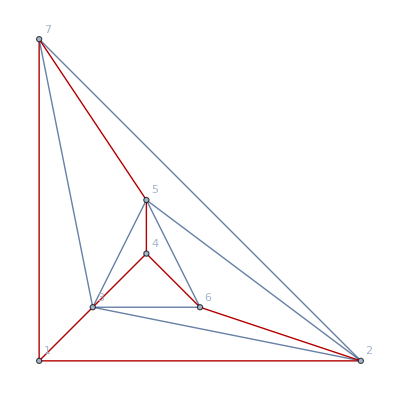

```mathematica
With[{g=Graph[ReadGrof[5],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Graph[g,GraphHighlight-> CollectMPGEdges[g]]]
```

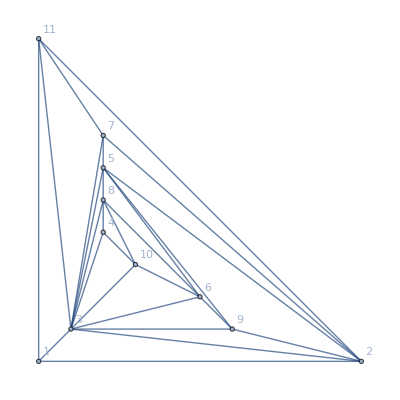
-Graphics-24

```mathematica
With[{g=Graph[ReadGrof[1386],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Labeled[Graph[g,GraphHighlight-> CollectMPGEdges[g]],ChromaticPolynomial[g,4]]]
```

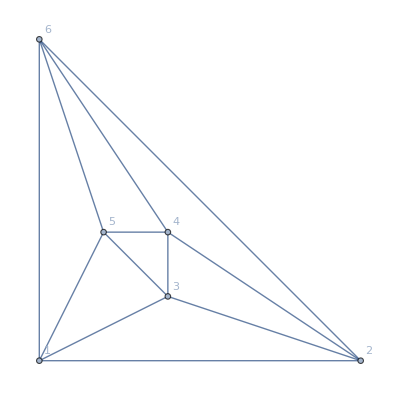
-Graphics-4

```mathematica
With[{g=Graph[ReadGrof[4],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Labeled[Graph[g,GraphHighlight-> CollectMPGEdges[g]],ChromaticPolynomial[g,4]/24]]
```

```mathematica
Factor[ChromaticPolynomial[ReadGrof[4],x]]
```

(-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)

```mathematica
Factor[ChromaticPolynomial[ReadGrof[12],x]]
```

(-3+x)^5 (-2+x) (-1+x) x

```mathematica
Factor[ChromaticPolynomial[ReadGrof[6],x]]
```

(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)

```mathematica
CompleteBaseCoeff[-32+29 x-9 x^2+x^3]
```

{-32,21,-6,1}

```mathematica
CompleteBaseCoeff[(-3+x) (-2+x)(-1+x)x]
```

{0,0,0,0,1}

```mathematica
FactorList[(-3+x) (-2+x)(-1+x)x]
```

{{1,1},{-3+x,1},{-2+x,1},{-1+x,1},{x,1}}

```mathematica
Table[CompleteBaseCoeff[k[[1]]^k[[2]]],{k,FactorList[(-3+x) (-2+x)(-1+x)x]}]
```

{{1},{-3,1},{-2,1},{-1,1},{0,1}}

```mathematica
CompleteBaseCoeff[(-1+x)x]
```

{0,0,1}

```mathematica
Table[k[[1]]^k[[2]],{k,FactorList[(-3+x) (-2+x)(-1+x)x]}]
```

{1,-3+x,-2+x,-1+x,x}

```mathematica
Degree[-398+553 x-317 x^2+95 x^3-15 x^4+x^5]
```

°[-398+553 x-317 x^2+95 x^3-15 x^4+x^5]

```mathematica
UniqueFactors[f_]:=Map[First,FactorList[f]]
```

```mathematica
Select[Range[1000],MemberQ[UniqueFactors[ChromaticPolynomial[ReadGrof[#],x]],119-133 x+58 x^2-12 x^3+x^4]&]
```

{18,36,38,88,94,99,109,113,123,159,172,187,188,196,197,217,220,221,222,223,346,347,381,386,387,389,391,410,411,431,456,463,477,483,510,511,523,538,550,564,585,594,595,596,597,598,599,600,601,616,620,628,657,661,662,663,664,665,694,698,708,718,719,720,721,722,725,727,753,777,785,790,801,805,815,834,835,836,837,838,839,840,841,842,856,873,882,883,890,891,895,906}

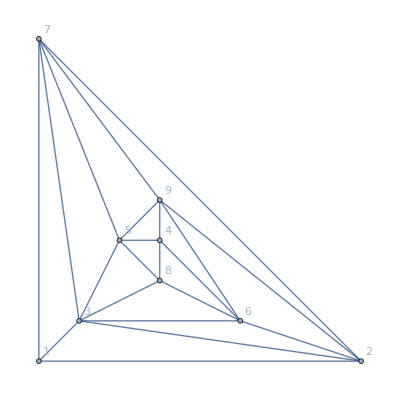
-Graphics-3

```mathematica
With[{g=Graph[ReadGrof[36],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Labeled[Graph[g,GraphHighlight-> CollectMPGEdges[g]],ChromaticPolynomial[g,4]/24]]
```

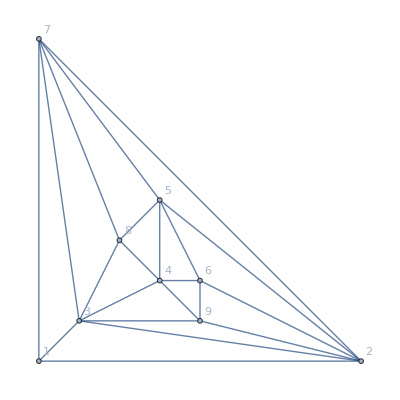
-Graphics-3

```mathematica
With[{g=Graph[ReadGrof[38],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Labeled[Graph[g,GraphHighlight-> CollectMPGEdges[g]],ChromaticPolynomial[g,4]/24]]
```

```mathematica
IsomorphicGraphQ[ReadGrof[36],ReadGrof[38]]
```

False

```mathematica
Factor[ChromaticPolynomial[ReadGrof[88],x]]
```

(-3+x)^3 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4)

```mathematica
Factor[ChromaticPolynomial[ReadGrof[38],x]]
```

(-3+x)^2 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4)

```mathematica
Table[
UniqueFactors[ChromaticPolynomial[ReadGrof[k],x]],{k,Select[Range[1000],MemberQ[UniqueFactors[ChromaticPolynomial[ReadGrof[#],x]],119-133 x+58 x^2-12 x^3+x^4]&]}
]//DeleteDuplicates
```

{{1,-3+x,-2+x,-1+x,x,119-133 x+58 x^2-12 x^3+x^4},{1,-3+x,-2+x,-1+x,x,-32+29 x-9 x^2+x^3,119-133 x+58 x^2-12 x^3+x^4}}

```mathematica
Select[Range[1000],With[{f=UniqueFactors[ChromaticPolynomial[ReadGrof[#],x]]},MemberQ[f,-32+29 x-9 x^2+x^3]&&MemberQ[f,119-133 x+58 x^2-12 x^3+x^4]]&]
```

{456,708}

```mathematica
Select[Range[1000],With[{f=UniqueFactors[ChromaticPolynomial[ReadGrof[#],x]]},MemberQ[f,-32+29 x-9 x^2+x^3]]&]
```

{4,6,14,15,19,20,25,30,35,49,56,57,62,63,64,65,66,67,78,79,82,93,95,96,97,98,101,102,103,104,105,106,111,125,134,136,145,147,151,158,161,162,163,164,165,166,167,168,169,186,189,195,201,241,245,249,250,251,252,253,254,255,271,273,278,281,282,283,284,285,286,287,295,296,297,298,299,300,301,302,308,309,312,313,318,321,345,348,350,351,356,357,359,383,384,414,415,418,419,421,439,443,444,445,446,447,448,449,450,451,452,453,454,455,456,459,460,461,462,466,467,468,469,470,471,472,473,474,475,476,480,481,491,503,504,505,506,507,508,528,541,558,571,575,577,587,619,638,644,646,649,650,651,652,653,654,655,668,669,670,673,674,675,676,677,678,681,682,683,684,685,686,687,688,689,690,691,692,696,697,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,741,742,743,744,745,746,747,748,749,750,751,755,756,757,758,759,760,761,762,763,764,765,766,767,768,771,772,773,774,778,779,780,781,786,787,802,806,817,818,819,820,907,912,913,926,927,928,929,930,931,932,933,934,935,936,937,966,976,984,987,992}

```mathematica
Select[Range[1000],With[{f=UniqueFactors[ChromaticPolynomial[ReadGrof[#],x]]},MemberQ[f,119-133 x+58 x^2-12 x^3+x^4]]&]
```

{18,36,38,88,94,99,109,113,123,159,172,187,188,196,197,217,220,221,222,223,346,347,381,386,387,389,391,410,411,431,456,463,477,483,510,511,523,538,550,564,585,594,595,596,597,598,599,600,601,616,620,628,657,661,662,663,664,665,694,698,708,718,719,720,721,722,725,727,753,777,785,790,801,805,815,834,835,836,837,838,839,840,841,842,856,873,882,883,890,891,895,906}

```mathematica
Factor[ChromaticPolynomial[ReadGrof[4],x]]
```

(-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)

```mathematica
With[{g=Graph[ReadGrof[4],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Labeled[Graph[g,GraphHighlight-> CollectMPGEdges[g]],{Factor[ChromaticPolynomial[g,x]],ChromaticPolynomial[g,4]/24}]]
```

-Graphics-{(-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),4}

```mathematica
CalculateInOutFormulaMany[ReadGrof[4],{{3,4,5},{2}}]
```

-4 B2+A3 B2+A3x4x5 B2-A3x5 B2+A4 B2-A4x5 B2+2 A5 B2

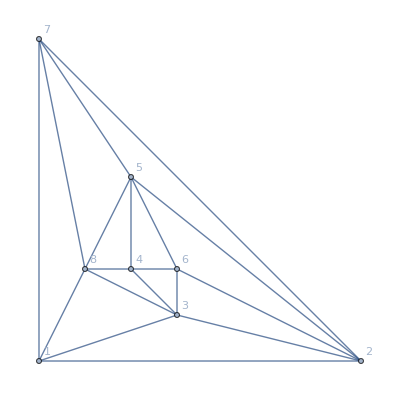
-Graphics-3

```mathematica
With[{g=Graph[ReadGrof[18],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Labeled[Graph[g,GraphHighlight-> CollectMPGEdges[g]],ChromaticPolynomial[g,4]/24]]
```

```mathematica
Factor[ChromaticPolynomial[ReadGrof[456],x]]
```

(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3) (119-133 x+58 x^2-12 x^3+x^4)

```mathematica
Factor[ChromaticPolynomial[ReadGrof[708],x]]
```

(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3) (119-133 x+58 x^2-12 x^3+x^4)

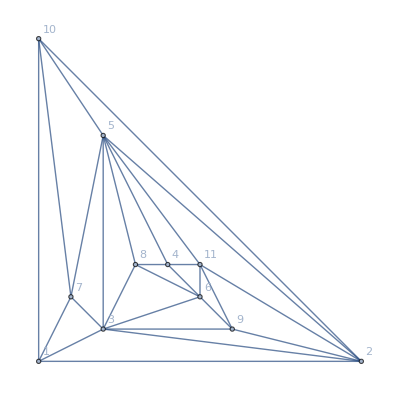
-Graphics-12

```mathematica
With[{g=Graph[ReadGrof[456],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Labeled[Graph[g,GraphHighlight-> CollectMPGEdges[g]],ChromaticPolynomial[g,4]/24]]
```

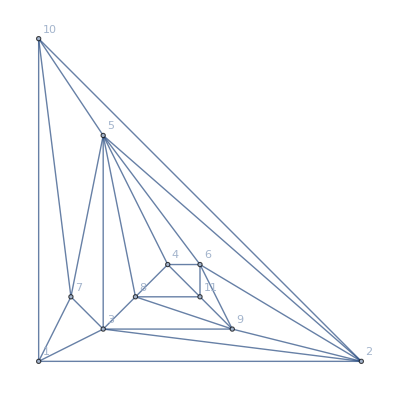
-Graphics-12

```mathematica
With[{g=Graph[ReadGrof[708],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]},Labeled[Graph[g,GraphHighlight-> CollectMPGEdges[g]],ChromaticPolynomial[g,4]/24]]
```

```mathematica
Factor[ChromaticPolynomial[ReadGrof[456],x]]
```

```mathematica
Select[Table[{Length[FactorList[-11587640+36201540 x-53536411 x^2+49825808 x^3-32648195 x^4+15922746 x^5-5944840 x^6+1718041 x^7-383551 x^8+65178 x^9-8175 x^10+715 x^11-39 x^12+x^13+k ]],k},{k,-100,100}],#[[1]]≠2&]
```

{{3,-40},{3,-4}}

```mathematica
Monitor[Sort[DeleteDuplicates[Flatten[Table[UniqueFactors[ChromaticPolynomial[Graph[plantri[[k]]],x]],{k,10}]]],Exponent[#1,x]<Exponent[#2,x]&],k]//TableForm
```

1
x
-1+x
-2+x
-3+x
20170-40240 x+36408 x^2-19698 x^3+6999 x^4-1670 x^5+260 x^6-24 x^7+x^8
254640-624395 x+710277 x^2-496739 x^3+237370 x^4-81028 x^5+19972 x^6-3498 x^7+415 x^8-30 x^9+x^10
-916328+2446742 x-3056481 x^2+2370977 x^3-1273217 x^4+497397 x^5-144062 x^6+30852 x^7-4772 x^8+506 x^9-33 x^10+x^11
3102974-9118081 x+12589635 x^2-10844568 x^3+6508871 x^4-2871562 x^5+954841 x^6-240835 x^7+45640 x^8-6322 x^9+606 x^10-36 x^11+x^12
3278599-9484411 x+12920696 x^2-11013474 x^3+6561868 x^4-2881964 x^5+956074 x^6-240914 x^7+45642 x^8-6322 x^9+606 x^10-36 x^11+x^12
3335190-9601930 x+13026427 x^2-11066898 x^3+6578227 x^4-2884995 x^5+956388 x^6-240928 x^7+45642 x^8-6322 x^9+606 x^10-36 x^11+x^12
-11587640+36201540 x-53536411 x^2+49825808 x^3-32648195 x^4+15922746 x^5-5944840 x^6+1718041 x^7-383551 x^8+65178 x^9-8175 x^10+715 x^11-39 x^12+x^13
-11517552+36057956 x-53414584 x^2+49771422 x^3-32635151 x^4+15921425 x^5-5944916 x^6+1718071 x^7-383553 x^8+65178 x^9-8175 x^10+715 x^11-39 x^12+x^13
-11877662+36882093 x-54248780 x^2+50261369 x^3-32818907 x^4+15966933 x^5-5952318 x^6+1718826 x^7-383596 x^8+65179 x^9-8175 x^10+715 x^11-39 x^12+x^13
-12001168+37166136 x-54538064 x^2+50431851 x^3-32882479 x^4+15982282 x^5-5954659 x^6+1719032 x^7-383604 x^8+65179 x^9-8175 x^10+715 x^11-39 x^12+x^13

```mathematica
Monitor[Sort[DeleteDuplicates[Flatten[Table[UniqueFactors[ChromaticPolynomial[ReadGrof[k],x]],{k,10000}]]],Exponent[#1,x]<Exponent[#2,x]&],k]//TableForm
```

1
x
-1+x
-2+x
-3+x
10-6 x+x^2
7-5 x+x^2
-49+38 x-10 x^2+x^3
-35+30 x-9 x^2+x^3
-32+29 x-9 x^2+x^3
119-133 x+58 x^2-12 x^3+x^4
-465+612 x-335 x^2+97 x^3-15 x^4+x^5
-438+585 x-326 x^2+96 x^3-15 x^4+x^5
-447+591 x-327 x^2+96 x^3-15 x^4+x^5
-422+570 x-320 x^2+95 x^3-15 x^4+x^5
-398+553 x-317 x^2+95 x^3-15 x^4+x^5
-383+542 x-315 x^2+95 x^3-15 x^4+x^5
-332+498 x-303 x^2+94 x^3-15 x^4+x^5
1501-2388 x+1640 x^2-628 x^3+142 x^4-18 x^5+x^6
1569-2450 x+1659 x^2-630 x^3+142 x^4-18 x^5+x^6
1390-2285 x+1609 x^2-625 x^3+142 x^4-18 x^5+x^6
1459-2350 x+1629 x^2-627 x^3+142 x^4-18 x^5+x^6
1454-2330 x+1608 x^2-619 x^3+141 x^4-18 x^5+x^6
1385-2265 x+1588 x^2-617 x^3+141 x^4-18 x^5+x^6
1271-2152 x+1551 x^2-613 x^3+141 x^4-18 x^5+x^6
1199-2077 x+1525 x^2-610 x^3+141 x^4-18 x^5+x^6
1496-2368 x+1619 x^2-620 x^3+141 x^4-18 x^5+x^6
-4442+8640 x-7351 x^2+3560 x^3-1064 x^4+197 x^5-21 x^6+x^7
-5323+9708 x-7840 x^2+3661 x^3-1072 x^4+197 x^5-21 x^6+x^7
-4475+8690 x-7382 x^2+3569 x^3-1065 x^4+197 x^5-21 x^6+x^7
-5488+9892 x-7916 x^2+3675 x^3-1073 x^4+197 x^5-21 x^6+x^7
-5635+10055 x-7984 x^2+3688 x^3-1074 x^4+197 x^5-21 x^6+x^7
-5172+9531 x-7762 x^2+3646 x^3-1071 x^4+197 x^5-21 x^6+x^7
-5442+9840 x-7895 x^2+3672 x^3-1073 x^4+197 x^5-21 x^6+x^7
-4318+8493 x-7292 x^2+3552 x^3-1064 x^4+197 x^5-21 x^6+x^7
-5562+9976 x-7954 x^2+3684 x^3-1074 x^4+197 x^5-21 x^6+x^7
-4803+9093 x-7567 x^2+3607 x^3-1068 x^4+197 x^5-21 x^6+x^7
-5370+9765 x-7869 x^2+3669 x^3-1073 x^4+197 x^5-21 x^6+x^7
-5127+9483 x-7745 x^2+3644 x^3-1071 x^4+197 x^5-21 x^6+x^7
-4847+9137 x-7580 x^2+3608 x^3-1068 x^4+197 x^5-21 x^6+x^7
-5248+9622 x-7805 x^2+3656 x^3-1072 x^4+197 x^5-21 x^6+x^7
-5048+9381 x-7693 x^2+3632 x^3-1070 x^4+197 x^5-21 x^6+x^7
-5053+9401 x-7714 x^2+3640 x^3-1071 x^4+197 x^5-21 x^6+x^7
-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7
-4603+8855 x-7465 x^2+3589 x^3-1067 x^4+197 x^5-21 x^6+x^7
-4925+9235 x-7628 x^2+3619 x^3-1069 x^4+197 x^5-21 x^6+x^7
-3195+6880 x-6387 x^2+3310 x^3-1035 x^4+196 x^5-21 x^6+x^7
-4043+8086 x-7040 x^2+3470 x^3-1050 x^4+196 x^5-21 x^6+x^7
-4508+8685 x-7329 x^2+3532 x^3-1055 x^4+196 x^5-21 x^6+x^7
-4712+8939 x-7448 x^2+3557 x^3-1057 x^4+196 x^5-21 x^6+x^7
-3907+7891 x-6930 x^2+3441 x^3-1047 x^4+196 x^5-21 x^6+x^7
-4382+8529 x-7258 x^2+3518 x^3-1054 x^4+196 x^5-21 x^6+x^7
-3962+7978 x-6986 x^2+3458 x^3-1049 x^4+196 x^5-21 x^6+x^7
-3695+7610 x-6794 x^2+3413 x^3-1045 x^4+196 x^5-21 x^6+x^7
-4247+8337 x-7149 x^2+3489 x^3-1051 x^4+196 x^5-21 x^6+x^7
-4910+9170 x-7545 x^2+3574 x^3-1058 x^4+196 x^5-21 x^6+x^7
-5228+9537 x-7701 x^2+3603 x^3-1060 x^4+196 x^5-21 x^6+x^7
-4832+9072 x-7497 x^2+3563 x^3-1057 x^4+196 x^5-21 x^6+x^7
-4298+8408 x-7188 x^2+3499 x^3-1052 x^4+196 x^5-21 x^6+x^7
-4583+8770 x-7361 x^2+3536 x^3-1055 x^4+196 x^5-21 x^6+x^7
-5033+9316 x-7610 x^2+3587 x^3-1059 x^4+196 x^5-21 x^6+x^7
-3152+6787 x-6301 x^2+3269 x^3-1025 x^4+195 x^5-21 x^6+x^7
-3728+7603 x-6734 x^2+3371 x^3-1034 x^4+195 x^5-21 x^6+x^7
14314-31915 x+31668 x^2-18337 x^3+6800 x^4-1658 x^5+260 x^6-24 x^7+x^8
12311-28701 x+29601 x^2-17670 x^3+6692 x^4-1651 x^5+260 x^6-24 x^7+x^8
15179-33341 x+32647 x^2-18687 x^3+6865 x^4-1663 x^5+260 x^6-24 x^7+x^8
12575-29200 x+29999 x^2-17835 x^3+6727 x^4-1654 x^5+260 x^6-24 x^7+x^8
15764-34199 x+33141 x^2-18826 x^3+6884 x^4-1664 x^5+260 x^6-24 x^7+x^8
14201-31824 x+31701 x^2-18390 x^3+6818 x^4-1660 x^5+260 x^6-24 x^7+x^8
14810-32780 x+32306 x^2-18583 x^3+6849 x^4-1662 x^5+260 x^6-24 x^7+x^8
11279-26977 x+28454 x^2-17291 x^3+6630 x^4-1647 x^5+260 x^6-24 x^7+x^8
13589-30858 x+31090 x^2-18196 x^3+6787 x^4-1658 x^5+260 x^6-24 x^7+x^8
12179-28531 x+29541 x^2-17676 x^3+6699 x^4-1652 x^5+260 x^6-24 x^7+x^8
20170-40240 x+36408 x^2-19698 x^3+6999 x^4-1670 x^5+260 x^6-24 x^7+x^8
17966-37309 x+34866 x^2-19293 x^3+6945 x^4-1667 x^5+260 x^6-24 x^7+x^8
15386-33596 x+32739 x^2-18685 x^3+6858 x^4-1662 x^5+260 x^6-24 x^7+x^8
14795-32715 x+32223 x^2-18538 x^3+6838 x^4-1661 x^5+260 x^6-24 x^7+x^8
14561-32343 x+31981 x^2-18457 x^3+6824 x^4-1660 x^5+260 x^6-24 x^7+x^8
17834-37130 x+34773 x^2-19271 x^3+6943 x^4-1667 x^5+260 x^6-24 x^7+x^8
18524-38068 x+35276 x^2-19405 x^3+6961 x^4-1668 x^5+260 x^6-24 x^7+x^8
15749-34134 x+33058 x^2-18781 x^3+6873 x^4-1663 x^5+260 x^6-24 x^7+x^8
16691-35510 x+33859 x^2-19014 x^3+6907 x^4-1665 x^5+260 x^6-24 x^7+x^8
16115-34685 x+33393 x^2-18884 x^3+6889 x^4-1664 x^5+260 x^6-24 x^7+x^8
17264-36325 x+34319 x^2-19143 x^3+6925 x^4-1666 x^5+260 x^6-24 x^7+x^8
14914-32835 x+32235 x^2-18515 x^3+6829 x^4-1660 x^5+260 x^6-24 x^7+x^8
16130-34750 x+33476 x^2-18929 x^3+6900 x^4-1665 x^5+260 x^6-24 x^7+x^8
16706-35575 x+33942 x^2-19059 x^3+6918 x^4-1666 x^5+260 x^6-24 x^7+x^8
17621-36843 x+34626 x^2-19237 x^3+6940 x^4-1667 x^5+260 x^6-24 x^7+x^8
17279-36390 x+34402 x^2-19188 x^3+6936 x^4-1667 x^5+260 x^6-24 x^7+x^8
14404-32062 x+31773 x^2-18380 x^3+6810 x^4-1659 x^5+260 x^6-24 x^7+x^8
15536-33850 x+32921 x^2-18753 x^3+6871 x^4-1663 x^5+260 x^6-24 x^7+x^8
17054-36051 x+34188 x^2-19116 x^3+6923 x^4-1666 x^5+260 x^6-24 x^7+x^8
18185-37625 x+35058 x^2-19357 x^3+6957 x^4-1668 x^5+260 x^6-24 x^7+x^8
15149-33211 x+32481 x^2-18597 x^3+6843 x^4-1661 x^5+260 x^6-24 x^7+x^8
13799-31123 x+31188 x^2-18195 x^3+6780 x^4-1657 x^5+260 x^6-24 x^7+x^8
14171-31694 x+31535 x^2-18300 x^3+6796 x^4-1658 x^5+260 x^6-24 x^7+x^8
16346-35047 x+33629 x^2-18964 x^3+6903 x^4-1665 x^5+260 x^6-24 x^7+x^8
13559-30728 x+30924 x^2-18106 x^3+6765 x^4-1656 x^5+260 x^6-24 x^7+x^8
13360-30250 x+30418 x^2-17818 x^3+6674 x^4-1641 x^5+259 x^6-24 x^7+x^8
-29012+81860 x-102981 x^2+75761 x^3-35913 x^4+11381 x^5-2415 x^6+332 x^7-27 x^8+x^9
-36212+96992 x-116339 x^2+82102 x^3-37620 x^4+11628 x^5-2430 x^6+332 x^7-27 x^8+x^9
-41108+106556 x-124125 x^2+85487 x^3-38450 x^4+11737 x^5-2436 x^6+332 x^7-27 x^8+x^9
-45860+115520 x-131190 x^2+88471 x^3-39164 x^4+11829 x^5-2441 x^6+332 x^7-27 x^8+x^9

```mathematica
(x-3)*(x-2)+1//Expand
```

7-5 x+x^2

```mathematica
(x-3)((x-3)*(x-2)+1)//Expand
```

-21+22 x-8 x^2+x^3

```mathematica
Factor[-49+38 x-10 x^2+x^3-(x-2)(x-3)]
```

-55+43 x-11 x^2+x^3

```mathematica
Select[Table[{Length[FactorList[119-133 x+58 x^2-12 x^3+x^4+k]],k},{k,-100,100}],#[[1]]≠2&]
```

{{3,-33},{3,-29},{3,-5},{3,-3},{3,1},{3,7}}

```mathematica
Factor[119-133 x+58 x^2-12 x^3+x^4+1]
```

(-3+x) (-40+31 x-9 x^2+x^3)

```mathematica
FullSimplify[(-3+x) (-40+31 x-9 x^2+x^3)]
```

(-3+x) (-40+x (31+(-9+x) x))

```mathematica
Factor[ (-40+31 x-9 x^2+x^3)+1]
```

(-3+x) (13-6 x+x^2)

```mathematica
Factor[ (13-6 x+x^2)-8]
```

(-5+x) (-1+x)

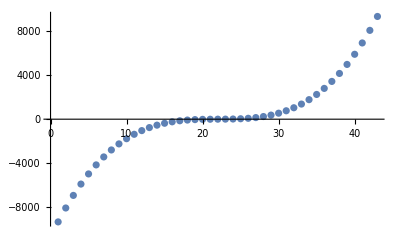

```mathematica
Map[Last,Select[Table[{Length[FactorList[(-40+31 x-9 x^2+x^3)+k]],k},{k,-10000,10000}],#[[1]]≠2&]]//ListPlot
```

```mathematica
Select[Table[{Length[FactorList[(13-6 x+x^2)+k]],k},{k,-10000,10000}],#[[1]]≠2&]
```

{{3,-9805},{3,-9608},{3,-9413},{3,-9220},{3,-9029},{3,-8840},{3,-8653},{3,-8468},{3,-8285},{3,-8104},{3,-7925},{3,-7748},{3,-7573},{3,-7400},{3,-7229},{3,-7060},{3,-6893},{3,-6728},{3,-6565},{3,-6404},{3,-6245},{3,-6088},{3,-5933},{3,-5780},{3,-5629},{3,-5480},{3,-5333},{3,-5188},{3,-5045},{3,-4904},{3,-4765},{3,-4628},{3,-4493},{3,-4360},{3,-4229},{3,-4100},{3,-3973},{3,-3848},{3,-3725},{3,-3604},{3,-3485},{3,-3368},{3,-3253},{3,-3140},{3,-3029},{3,-2920},{3,-2813},{3,-2708},{3,-2605},{3,-2504},{3,-2405},{3,-2308},{3,-2213},{3,-2120},{3,-2029},{3,-1940},{3,-1853},{3,-1768},{3,-1685},{3,-1604},{3,-1525},{3,-1448},{3,-1373},{3,-1300},{3,-1229},{3,-1160},{3,-1093},{3,-1028},{3,-965},{3,-904},{3,-845},{3,-788},{3,-733},{3,-680},{3,-629},{3,-580},{3,-533},{3,-488},{3,-445},{3,-404},{3,-365},{3,-328},{3,-293},{3,-260},{3,-229},{3,-200},{3,-173},{3,-148},{3,-125},{3,-104},{3,-85},{3,-68},{3,-53},{3,-40},{3,-29},{3,-20},{3,-13},{3,-8},{3,-5}}

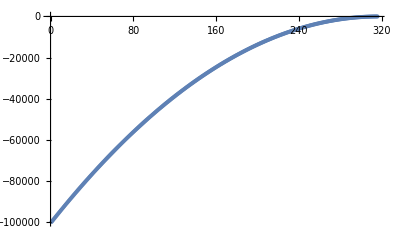

```mathematica
Map[Last,Select[Table[{Length[FactorList[(13-6 x+x^2)+k]],k},{k,-100000,100000}],#[[1]]≠2&]]//ListPlot
```

```mathematica
four=119-133 x+58 x^2-12 x^3+x^4
```

119-133 x+58 x^2-12 x^3+x^4

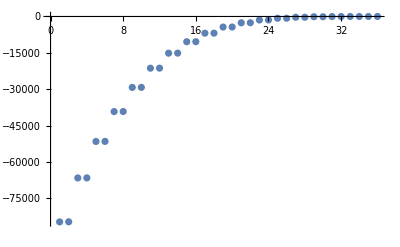

```mathematica
Map[Last,Select[Table[{Length[FactorList[four+k]],k},{k,-100000,100000}],#[[1]]≠2&]]//ListPlot
```

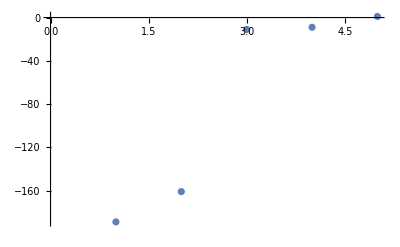

```mathematica
Map[Last,Select[Table[{Length[FactorList[1199-2077 x+1525 x^2-610 x^3+141 x^4-18 x^5+x^6+k]],k},{k,-1000,1000}],#[[1]]≠2&]]//ListPlot
```

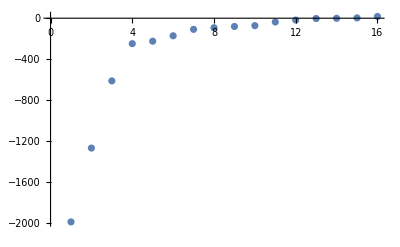

```mathematica
Map[Last,Select[Table[{Length[FactorList[(-40+31 x-9 x^2+x^3)+k x]],k},{k,-10000,10000}],#[[1]]≠2&]]//ListPlot
```

```mathematica
Select[Table[{Length[FactorList[(-40+31 x-9 x^2+x^3)+k x]],k},{k,-10000,10000}],#[[1]]≠2&]
```

{{3,-1992},{3,-1270},{3,-613},{3,-249},{3,-225},{3,-172},{3,-109},{3,-93},{3,-81},{3,-73},{3,-37},{3,-18},{3,-3},{3,-1},{3,3},{3,17}}

```mathematica
Select[Table[{Length[FactorList[four+k x]],k},{k,-10000,10000}],#[[1]]≠2&]
```

{{3,-2305},{3,-45},{3,-33},{3,323},{3,1487},{3,9507}}

```mathematica
Select[Table[{Length[FactorList[four+k ]],k},{k,-10000,10000}],#[[1]]≠2&]
```

{{3,-6893},{3,-6875},{3,-4359},{3,-4343},{3,-2603},{3,-2589},{3,-1445},{3,-1433},{3,-729},{3,-719},{3,-323},{3,-315},{3,-119},{3,-113},{3,-33},{3,-29},{3,-5},{3,-3},{3,1},{3,7}}

```mathematica
TableForm[Table[FactorList[four+-33  x^exp],{exp,0,8}],TableDepth->1]
```

{{1,1},{-1+x,1},{-86+47 x-11 x^2+x^3,1}}
{{1,1},{-1+x,1},{-119+47 x-11 x^2+x^3,1}}
{{1,1},{-1+x,1},{-119+14 x-11 x^2+x^3,1}}
{{1,1},{-1+x,1},{-119+14 x-44 x^2+x^3,1}}
{{-1,1},{-1+x,1},{119-14 x+44 x^2+32 x^3,1}}
{{-1,1},{-1+x,1},{119-14 x+44 x^2+32 x^3+33 x^4,1}}
{{-1,1},{-1+x,1},{119-14 x+44 x^2+32 x^3+33 x^4+33 x^5,1}}
{{-1,1},{-1+x,1},{119-14 x+44 x^2+32 x^3+33 x^4+33 x^5+33 x^6,1}}
{{-1,1},{-1+x,1},{119-14 x+44 x^2+32 x^3+33 x^4+33 x^5+33 x^6+33 x^7,1}}